```mathematica
first :=ListPlot[{{2, 4},{4, 5},{6, 6},{7, 7},{10, 8},{11, 8},{14, 11},{17, 10},{20, 12}}]
```

```mathematica
f[x_] = a*x + b;
```

```mathematica
nodes := {2, 4, 6, 7, 10, 11, 14, 17, 20}
```

```mathematica
values := {4, 5, 6, 7, 8, 8, 11, 10 ,12}
```

```mathematica
sum = Sum[(f[nodes[[i]]] - values[[i]])^2, {i, 1, Length[nodes]}]
```

(-4+2 a+b)^2+(-5+4 a+b)^2+(-6+6 a+b)^2+(-7+7 a+b)^2+(-8+10 a+b)^2+(-8+11 a+b)^2+(-11+14 a+b)^2+(-10+17 a+b)^2+(-12+20 a+b)^2

```mathematica
Solve[{D[sum, a] == 0, D[sum, b] == 0}, {a, b}]
```

{{a→52/119,b→59/17}}

```mathematica
t[x_] = 52/119*x + 59/17
```

59/17+(52 x)/119

```mathematica
second :=Plot[t[x], {x, 2, 20}]
```

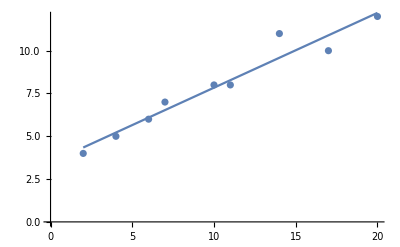

```mathematica
Show[first, second]
```